```mathematica
Clear["Global`*"]
(*name="student@10.0.1.9://home/student/BEM/Kramer2021_0d03/result.json"*)
data01DLPF4=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/LPF4/01D_LPF4.txt"}],"Data"];
data01DFNPF1=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Numerical_results/FNPF1/01D_FNPF1.txt"}],"Data"];
data01DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/01D_CI95_Normalized.txt"}],"Data"];
data03DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/03D_Measured1_Normalized.txt"}],"Data"];
data05DMeasured1Raw=Import[FileNameJoin[{ NotebookDirectory[],"Datafile/Experimental_results/05D_Measured1_Normalized.txt"}],"Data"];
name="~/BEM/Kramer2021_H00d03_small/result.json"
Quiet[Z=(data="float_COM"/.Import[name])[[;;,3]];];
Quiet[Vx=(data="float_velocity"/.Import[name])[[;;,1]];];
Quiet[Vy=(data="float_velocity"/.Import[name])[[;;,2]];];
Quiet[Vz=(data="float_velocity"/.Import[name])[[;;,3]];];
Quiet[time="time"/.Import[name];];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
H0=30/1000;
```

~/BEM/Kramer2021_H00d03_small/result.json

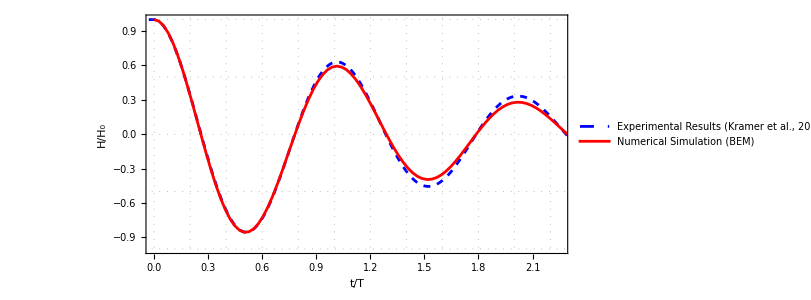

```mathematica
fig=ListPlot[
{
{#1(*/0.76*),#2(*/H0*)}&@@@data01DMeasured1Raw[[2;;]],
{(time-0.02)/0.76,(Z-((*-34.8+*)900)/1000)/H0}ᵀ
(*,{#1/0.76,#2/H0}&@@@data01DFNPF1[[2;;]]
,{#1/0.76,#2/H0}&@@@data01DLPF4[[2;;]]*)

},
Joined->{True,True},
PlotStyle->{{Blue,Dashed},Red},
BaseStyle->{FontFamily->"Times"},
PlotRange->{{0,2.25},{-1.,1.}},
AspectRatio->1/2,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},
Frame->True,
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["H/H_0",FontSize->20,FontFamily->"Times",Italic]},
FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted],
ImageSize->600,
PlotLegends->Placed[LineLegend[{"Experimental Results (Kramer et al., 2021)","Numerical Simulation (BEM)"},LegendMarkerSize->20,LabelStyle->15],{0.65,0.15}]
]
```

```mathematica
(*dir="/Users/tomoaki/Library/CloudStorage/Dropbox/meeting/海洋工学シンポジウム/2023/投稿論文/"*)
dir=NotebookDirectory[];
filename=dir<>"HH0_vs_tT20230901.pdf";
(*Export[filename,fig,"PDF"];*)
```

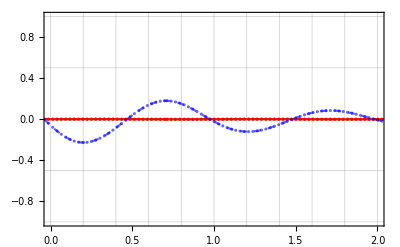

```mathematica
ListPlot[
{
{(time-0.05)/0.76,Vx}ᵀ,
{(time-0.05)/0.76,Vy}ᵀ,
{(time-0.05)/0.76,Vz}ᵀ
},
PlotStyle->{{Darker[Green],Opacity[0.6]},{Red},{Dashed,Blue,Opacity[0.6]},{Thick}},
Joined->{False,True,True,True},
PlotRange->{{0,2},{-1.,1.}},
PlotTheme->"Scientific",
Frame->True,
Mesh->All,
GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]}
]
```